{{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

{{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

0.00217573

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

NSolve solution: {{Tscale→25.4503}}

FindRoot::precw: The precision of the argument function («1»==0.01) is less than WorkingPrecision (100.).

Increased precision to ∞ at x = x

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{Tscale→33.99999999999999999999999999999999999999999999999999999999999999999999957602752271361622426231632487}

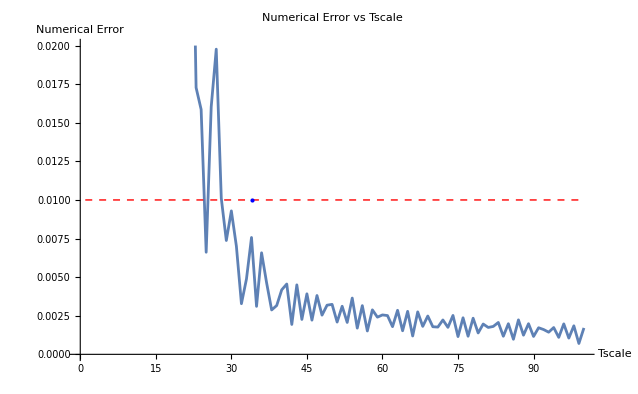

{Tscale→33.99999999999999999999999999999999999999999999999999999999999999999999957602752271361622426231632487}

```mathematica
Needs["NumericalCalculus`"]

initialTime=0;
endTime=25;
totalTime=endTime-initialTime;
dimension=4;
t1=1;
t2=1/Sqrt[2];
n=1000;
dt=0.01;

Tscale[T_]:=T

generateGOEMatrix[n_Integer]:=Module[{matrix},matrix=Table[If[i==j,RandomVariate[NormalDistribution[0,1]],RandomVariate[NormalDistribution[0,1/Sqrt[2]]]],{i,n},{j,n}];
matrix=(matrix+Transpose[matrix])/2;matrix]

H[t_,T_]:=Tscale[T]*((Sin[t/t1]*2.1+Sin[t/t2])*Hinitial+(Cos[t/t1]*2.7+Cos[t/t2])*Hend)

groundState[t_,T_]:=Module[{eigenvalues,eigenvectors,minIndex},{eigenvalues,eigenvectors}=Eigensystem[H[t,T]];
minIndex=First[Ordering[Re[eigenvalues],1]];
Normalize[Re[eigenvectors[[minIndex]]]]]

generateGroundStates[dt_,T_]:=Module[{t,states,currentState,nextState,dotProduct},states={groundState[initialTime,T]};
currentState=groundState[initialTime,T];
For[t=initialTime,t<endTime,t+=dt,nextState=groundState[t+dt,T];
dotProduct=Re[Dot[currentState,nextState]];
If[dotProduct>=0,AppendTo[states,nextState],AppendTo[states,-nextState]];
currentState=Last[states];];
states]

state[t_,n_,T_]:=Module[{eigenvalues,eigenvectors,index},{eigenvalues,eigenvectors}=Eigensystem[H[t,T]];
index=Ordering[Re[eigenvalues],n+1][[n+1]];
Normalize[Re[eigenvectors[[index]]]]]

generateExcitedStates[dt_,n_,T_]:=Module[{t,states,currentState,nextState,dotProduct},states={state[initialTime,n,T]};
currentState=state[initialTime,n,T];
For[t=initialTime,t<endTime,t+=dt,nextState=state[t+dt,n,T];
dotProduct=Re[Dot[currentState,nextState]];
If[dotProduct>=0,AppendTo[states,nextState],AppendTo[states,-nextState]];
currentState=Last[states];];
states]

gap[t_,n_,T_]:=Module[{eigenvalues,sortedEigenvalues,smallestEigenvalue,nEigenvalue,difference},eigenvalues=Re[Eigenvalues[H[t,T]]];
sortedEigenvalues=Sort[eigenvalues];
smallestEigenvalue=sortedEigenvalues[[1]];
nEigenvalue=sortedEigenvalues[[n+1]];
difference=nEigenvalue-smallestEigenvalue;
difference]

omega[n_,T_]:=NIntegrate[gap[t,n,T]/Tscale[T],{t,initialTime,endTime}]

derivativeGroundState[t_?NumericQ,T_,h_:0.01]:=(groundState[t+h,T]-groundState[t-h,T]*(groundState[t+h,T].groundState[t-h,T]))/(2*h)

normDerivativeGroundState[t_,T_]:=Norm[derivativeGroundState[t,T]]

Hinitial={{-0.978011,0.442537,-1.13173,-0.885678},{0.442537,-0.888185,-0.238622,0.40392},{-1.13173,-0.238622,1.04262,-0.563516},{-0.885678,0.40392,-0.563516,0.552724}}

Hend={{0.0482198,0.593326,-0.64427,0.680961},{0.593326,-0.00816359,-0.186093,-0.463839},{-0.64427,-0.186093,0.800334,0.700095},{0.680961,-0.463839,0.700095,0.545787}}

calculateNumericalError[T_]:=Module[{schrodingerEqu,initialCondition,sol,psiFunction,numericalError},schrodingerEqu=I D[psi[t],t]==H[t,T].psi[t];
initialCondition=psi[initialTime]==groundState[initialTime,T];
sol=NDSolve[{schrodingerEqu,initialCondition},psi,{t,initialTime,endTime}];
psiFunction=psi/. First[sol];
numericalError=Sqrt[Abs[1-Abs[groundState[endTime,T].psiFunction[endTime]]^2/Norm[psiFunction[endTime]]^2]];
numericalError]

calculateNumericalError[42.098]

startT = 1; (* dont start at 0*)
endT = 100;

Tscales=Range[startT,endT];
numericalErrors=Table[calculateNumericalError[T],{T,Tscales}];

errorInterpolation=Interpolation[Transpose[{Tscales,numericalErrors}]];
Error[Tscale_]:=errorInterpolation[Tscale]

Print["NSolve solution: ", NSolve[Error[Tscale]==0.01,Tscale, MaxRoots->3]]

lastTscale= Block[{prec=MachinePrecision},FindRoot[Error[Tscale]==0.01,{Tscale,endT/2.},AccuracyGoal->Infinity,PrecisionGoal->8, WorkingPrecision->100,StepMonitor:>If[Precision[x]≠prec,prec=Precision[x];Print["Increased precision to ",prec," at x = ",x];]]]

ListLinePlot[Transpose[{Tscales,numericalErrors}],PlotRange->{0,0.02},Epilog->{Red,Dashed,Line[{{startT,0.01},{endT,0.01}}],Blue,PointSize[Medium],Point[{Tscale/. lastTscale,0.01}]},PlotLabel->"Numerical Error vs Tscale",AxesLabel->{"Tscale","Numerical Error"}]

lastTscale
```